# Other Topics

## Ncdf

### Different Ways To Evaluate N(x) in Mathematica

```mathematica
(* built-in functions *)
Ncdf0[x_]:=(1+Erf[x/(√2)])/2;
Ncdf1[x_]:=CDF[NormalDistribution[0, 1],x];

(* see John Hull *)
Ncdf2[x_]:=Block[{p, sg, a1, a2, a3, a4, a5},
a1=0.319381530;
a2=-0.356563782;
a3=1.781477937;
a4=-1.821255978;
a5=1.330274429;

sg=Sign[Re[x]];
p=1/(1+sg 0.2316419 x);
Return[0.5+0.5sg-sg 1/(√(2π))ⅇ^(-x^2/2)p (a1+p (a2+p (a3+p (a4+a5 p))))]
];


a=RandomReal[]

Ncdf0[a]
Ncdf1[a]
Ncdf2[a]
```

0.590566

0.722594

0.722594

0.722594

### Notes on Error & Efficiency

Using built-in function, one can obtain almost exact values. 
In constrast, the widely used approximation could introduce an errof of 10^-7, as shown in the figure. 
But, as experiments show us, using built-in functions to evaluate N(x) is very inefficient. 
If an algorithm involves N(x) frequently, and if one can withstand an error of 10^-7, the widely used approximation is a better choice.

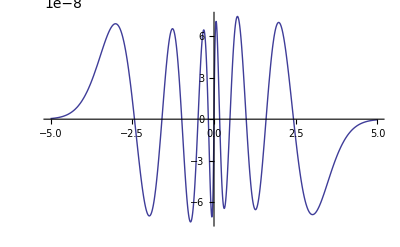

```mathematica
Clear[Ncdf0, Ncdf1, Ncdf2, Ncdf];

Ncdf[x_]:=Block[{p, sg, a1, a2, a3, a4, a5},
a1=0.319381530;
a2=-0.356563782;
a3=1.781477937;
a4=-1.821255978;
a5=1.330274429;

sg=Sign[Re[x]];
p=1/(1+sg 0.2316419 x);
Return[0.5+0.5sg-sg 1/(√(2π))ⅇ^(-x^2/2)p (a1+p (a2+p (a3+p (a4+a5 p))))]
];
Plot[Ncdf[x]-(1+Erf[x/(√2)])/2, {x, -5, 5}]
```

### More Efficiently

Recently I designed an algorithm that evaluates N(x) really frequently. 
In this case, both of the above are not the best choice. 
If one can withstand an error of 10^-7, keeping 1201 exact values of N(x) between [-6, 6] and using qudratic interpolation will work more efficiently. 
When x is out of the interval [-6, 6], we set N(x) to 0 or 1. 
The error caused in this part this is, as shown in the following computations, always less than 10^-9. 

Besides, althought the error due to qudratic interpolations depends on the derivative of N(x), as shown in the figure, its absolute value is quite small.

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-5.99781}}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→5.99781}}

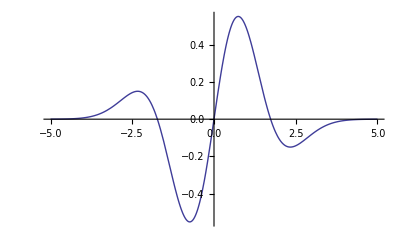

```mathematica
Ncdf[x_]:=(1+Erf[x/(√2)])/2;

NSolve[Ncdf[x]==10^-9, x]
NSolve[Ncdf[x]==1-10^-9, x]

Plot[Ncdf''''[x], {x, -5, 5}]
```

## Newton-Cotes Coefficients

### Integrating The Lagrange Basis Polynomials

```mathematica
Coeff[n_, j_]:=Block[{qq}, (* n 個點之中積前 j 個點的積分係數 *)
Table[
qq=Table[0, {n}];
qq[[k]]=1;

Integrate[
InterpolatingPolynomial[{Range[n], qq}//Transpose, x]
, {x, 1, j}]
, {k, 1, n}]//Return
]

Coeff[3, 3](* Simpson's rule *)
Coeff[5, 5](* Boole's rule *)
```

{1/3,4/3,1/3}

{14/45,64/45,8/15,64/45,14/45}

```mathematica
Coeff[5, 2](* imcomplete Boole *)
Coeff[5, 3](* imcomplete Boole *)
Coeff[5, 4](* imcomplete Boole *)
```

{251/720,323/360,-11/30,53/360,-19/720}

{29/90,62/45,4/15,2/45,-1/90}

{27/80,51/40,9/10,21/40,-3/80}

### Another Way to Generate Newton-Cotes Coefficients

Thanks to James Keesling.
We have another algorithm to generate Newton-Cotes Coefficients, rather than integrating the basis polynomials.

```mathematica
(* generate a Vandermonde Matrix *)
n=4;
V=Prepend[
Table[i^j, {i, 1, n}, {j, 0, n}], 
Prepend[Table[0, {n}], 1]
];
V//MatrixForm

(* solve the linear system *)
LinearSolve[
V//Transpose,(* Vandermonde taking transpose *)
Table[n^(i+1)/(i+1), {i, 0, n}]
]
```

(1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16
1 | 3 | 9 | 27 | 81
1 | 4 | 16 | 64 | 256)

{14/45,64/45,8/15,64/45,14/45}

## The Error Introduced by The Trapezoidal Rule, And The Simpson’ Rule

12/14/2010

The log-log plot shows that the trapezoidal rule has an error convergence rate of O(h^2), and the Simpson’s rule has an error convergence rate of O(h^4). 
The function of the line that best fits the points (log h, log |error|) is given.

-4.651848464618112362826212838186707685897+3.9999710887170406323002367439301706323808 x

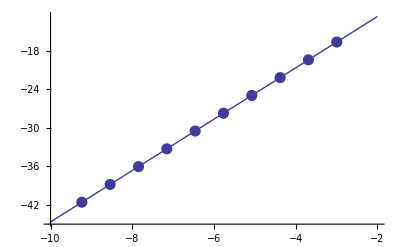

-1.943612102655945959303952874280602990498269491422+1.9999959521620188288846642327398805666544794625635 x

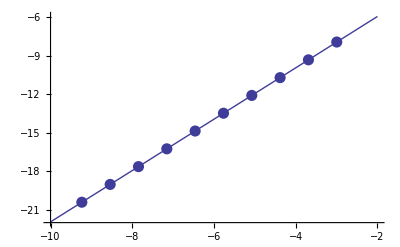

```mathematica
Simp[f_, n_, a_, b_]:= Block[{grids, tmp, coeff}, (* using simpson's rule to integrate f, from a to b *)
grids = Range[a, b, (b-a)/n];
tmp = Table[f[grids[[i]]], {i, 1, n+1}];
coeff = Table[If[OddQ[i], 4, 2], {i, 1, n-1}];
coeff = Prepend[coeff, 1];
coeff = Append[coeff, 1]/3;
N[tmp.coeff(b-a)/n, 60]//Return;
];

Trap[f_, n_, a_, b_]:= Block[{grids, tmp, coeff}, (* trapezoidal rule *)
grids = Range[a, b, (b-a)/n];
tmp = Table[f[grids[[i]]], {i, 1, n+1}];
coeff = Join[{1/2}, Table[1, {n-1}], {1/2}];
N[tmp.coeff(b-a)/n, 60]//Return;
];

f[x_]:=ⅇ^x;
a=0;
b=1;

exact = Integrate[f[x], {x, a, b}];

(* Simpson's rule *)
simppts=Table[{Log[1/(2^i 10)], Log[Abs[Simp[f, 2^i 10, a, b]-exact]]}, {i, 1, 10}];
Fit[simppts, {1, x}, x]
Show[Plot[%, {x, -10, -2}], ListPlot[simppts, PlotStyle->PointSize[.02]], ImageSize->400]

(* Trapezoidal rule *)
trappts=Table[{Log[1/(2^i 10)], Log[Abs[Trap[f, 2^i 10, a, b]-exact]]}, {i, 1, 10}];
Fit[trappts, {1, x}, x]
Show[Plot[%, {x, -10, -2}], ListPlot[trappts, PlotStyle->PointSize[.02]], ImageSize->400]
```